```mathematica
ClearAll["Global`*"]
```

```mathematica
g=9.8;
L=.4;
θ0=π/2;
τ=2.74;
c=0;
m=1;
time=10;
```

### Period for small θ

```mathematica
T=(2π)/(√(g/L))
```

1.2694

```mathematica
τ=m g L Sin[π/4]
```

2.77186

### Plot

```mathematica
dynamics=θ''[t]+c θ'[t]+g/L Sin[θ[t]]==τ/(m L^2);
ic={θ[0]==θ0,θ'[0]==0};
```

```mathematica
sol=NDSolve[{dynamics,ic},θ,{t,0,time}];
```

```mathematica
f[x_]:=Evaluate[θ[x]*180/π/.sol]
```

### Long term solution

```mathematica
f[time]
```

{89.784}

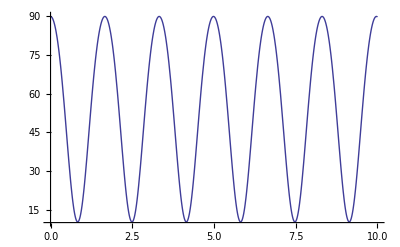

```mathematica
Plot[f[t],{t,0,time},PlotRange->All]
```